```mathematica
SetDirectory["/home/ethan/spring20/comphys/week5/coding"];
trunk =Flatten[Table[ReadList["!./linear "<>ToString[n] <>" " <> ToString[Round[n/2]] <>" " <> ToString[Round[n/2]] <>" " <> ToString[Round[n/2]+2]<>" " <> ToString[Round[n/2]+1]], {n,5, 21}]]
```

{0.966364,0.960674,0.959235,0.842013,0.812445,0.810065,0.808986,0.796566,0.790587,0.789467,0.788827,0.785233,0.783093,0.782489,0.782098,0.780603,0.779607}

```mathematica
Round[17/2]
```

8

```mathematica
"!./linear "<>ToString[n] <>" " <> ToString[Round[n/2]] <>" " <> ToString[Round[n/2]] <>" " <> ToString[Round[n/2]+2]<>" " <> ToString[Round[n/2]+1]
```

!./linear 5 2 2 4 3

```mathematica
donut = Table[{n,ReadList["!./p3 "<>ToString[n] <>" " <> ToString[Round[n/2]] <>" " <> ToString[Round[n/2]] <>" " <> ToString[Round[n/2]+2]<>" " <> ToString[Round[n/2]+1], Number][[1]]}, {n,5,21}]
```

{{5,0.68},{6,0.706746},{7,0.723705},{8,0.73501},{9,0.74288},{10,0.748564},{11,0.752797},{12,0.756031},{13,0.758557},{14,0.760566},{15,0.76219},{16,0.763521},{17,0.764626},{18,0.765553},{19,0.766338},{20,0.767009},{21,0.767586}}

```mathematica
trunk = Table[{n,ReadList["!./linear "<>ToString[n] <>" " <> ToString[Round[n/2]] <>" " <> ToString[Round[n/2]] <>" " <> ToString[Round[n/2]+2]<>" " <> ToString[Round[n/2]+1], Number][[1]]}, {n,5,21}]
```

{{5,0.966364},{6,0.960674},{7,0.959235},{8,0.842013},{9,0.812445},{10,0.810065},{11,0.808986},{12,0.796566},{13,0.790587},{14,0.789467},{15,0.788827},{16,0.785233},{17,0.783093},{18,0.782489},{19,0.782098},{20,0.780603},{21,0.779607}}

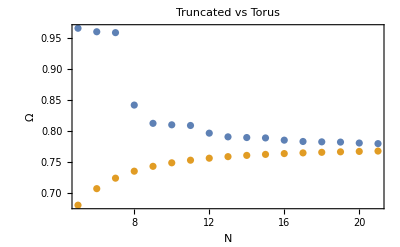

```mathematica
ListPlot[{trunk,donut},PlotRange->All, Frame->True, PlotLabel->"Truncated vs Torus", FrameLabel->{"N","Ω"}]
```

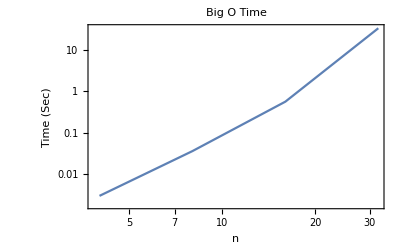

```mathematica
ListLogLogPlot[{{4, 0.003},{8,0.036},{16,0.560}, {32, 32.958}}, Frame->True, PlotLabel->"Big O Time", FrameLabel->{"n","Time (Sec)"}, Joined->True]
```